```mathematica
SetDirectory["/home/xidad/CLionProjects/DendriteV3/cmake-build-release"];
```

```mathematica
domain =SparseArray@Import["domain.txt","Table"];
data = SparseArray@Import["data.txt","Table"];
```

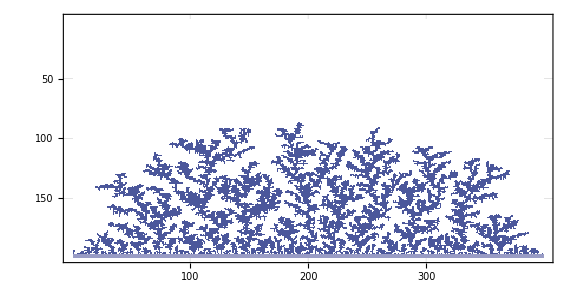

```mathematica
plt= MatrixPlot[data,ImageSize->Large,PlotTheme->"Scientific",GridLines->Automatic,MaxPlotPoints->Infinity,PlotRange->Automatic]
```

```mathematica
EP =Import["EP.txt","Table"];
(*EF=Import["EF.txt","Table"];*)
EP =Parallelize@Table[ Table[EP[[j,i]],{i,1,Length@EP[[1]]}],{j,Length@EP,1,-1}];
(*EF = Table[Table[{{i,j},{EF[[j,i]],EF[[j,i+1]]}},{i,1,Length@EF[[1]]/2,2}],{j,Length@EF,1,-1}];*)
```

```mathematica
epplt=ListContourPlot[EP,ImageSize->Large,PlotTheme->"Scientific",PlotRange->{Automatic,Automatic,{0,10}},PlotLegends->Automatic,ClippingStyle->Automatic(*,Contours->15*),AspectRatio->1/2]
```

-Graphics-

```mathematica
+
```

```mathematica
ListStreamPlot
```

```mathematica
Show[{
MatrixPlot[data,ImageSize->Large,PlotTheme->"Scientific",GridLines->Automatic,MaxPlotPoints->Infinity,PlotRange->Automatic],
ListContourPlot[EP,ImageSize->Large,PlotTheme->"Scientific",PlotRange->{Automatic,Automatic,{0,10}},PlotLegends->Automatic,ClippingStyle->Automatic,Contours->15]
}]
```

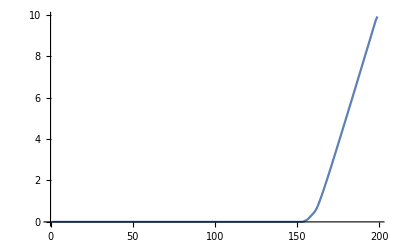

```mathematica
ListLinePlot[EP[[All,50]],PlotRange->Full]
```

```mathematica
ListVectorPlot[EF,VectorMarkers->"Drop",PlotTheme->"Scientific",AspectRatio->2,VectorScale->Automatic]
```

```mathematica
20/0.01*10/0.01
```

2.×10^6

```mathematica
2*^6 0.2
```

400000.

```mathematica
(10/0.01)^2 2
```

```mathematica
2.*^6.2
```

400000.

```mathematica
Table[Table[u[j+1,i]+u[j-1,i]+u[j,i+1]+u[j,i-1]==0,{i,0,2}],{j,0,2}]//MatrixForm
```

(u[-1,0]+u[0,-1]+u[0,1]+u[1,0]==0 | u[-1,1]+u[0,0]+u[0,2]+u[1,1]==0 | u[-1,2]+u[0,1]+u[0,3]+u[1,2]==0
u[0,0]+u[1,-1]+u[1,1]+u[2,0]==0 | u[0,1]+u[1,0]+u[1,2]+u[2,1]==0 | u[0,2]+u[1,1]+u[1,3]+u[2,2]==0
u[1,0]+u[2,-1]+u[2,1]+u[3,0]==0 | u[1,1]+u[2,0]+u[2,2]+u[3,1]==0 | u[1,2]+u[2,1]+u[2,3]+u[3,2]==0)

```mathematica
Export["tst.png",epplt]
```

tst.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["tst.png"]]]
```

```mathematica
SetDirectory["/home/xidad/CLionProjects/DendriteV3/pics"];
img = Import["d1.JPG"];
```

```mathematica
dim = ImageDimensions@img;
binImg = LocalAdaptiveBinarize[img,2,{0.9,0.5,0}];

thresImg = ImageTake[1-ImageAdjust@img,{dim[[1]]/2,dim[[1]]},{dim[[2]]/3,dim[[2]]2/3}];
thres = FindThreshold@thresImg;

cut = 1-ImageTake[img,{dim[[1]]/2,dim[[1]]},{dim[[2]]/3,dim[[2]]2/3}];

test =GaussianFilter[LocalAdaptiveBinarize[ColorConvert[ImageAdjust@Sharpen[cut,1000],"Grayscale"],2,{0.9,0,0.08FindThreshold@cut}],5]

cut
```

-Graphics-

-Graphics-

```mathematica
test2=-Graphics-;
```

```mathematica
ListLogLogPlot[result,PlotStyle->Red]
```

FittedModel[12.9791+2.07158 x]

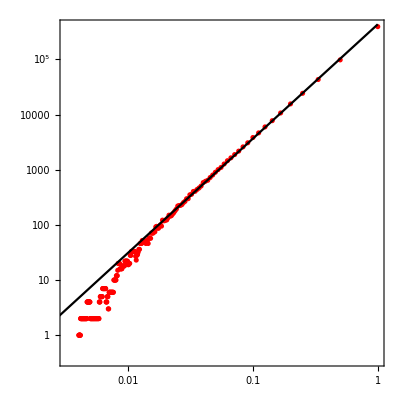

FittedModel[10.7107+1.78969 x]

$Aborted

```mathematica
Clear[result]
result[image_]:=Table[{1/eps,Last@First@ImageLevels@Image[BlockMap[Max,ImageData[image],{eps,eps}],"Bit"]},{eps,1,Max[Min[ImageDimensions@image],1],Max[Min[ImageDimensions@image]/1000,1]}];

result = result@test2;

fm=LinearModelFit[Log[result[[;;Floor[Length@result/10]]]],{1,x},x]
plot=Show[ListLogLogPlot[result,PlotStyle->Red,GridLines->Automatic],Plot[fm[x],{x,Log[(result)[[1,1]]],Log[(result)[[-1,1]]]},PlotStyle->Black],AspectRatio->1,Axes->False,Frame->True]
```

```mathematica
ClearAll@imgs
imgs[image_]:=Table[Image[BlockMap[Max,ImageData[image],{eps,eps}],"Bit"],{eps,1,Max[Min[ImageDimensions@image],1],Max[Min[ImageDimensions@image]/1000,1]}];
imgs = imgs@test;
sz =300;
imgs=If[First@ImageDimensions[#]>sz,ImageResize[Image[#,Real],sz],(*downscale as grayscale*)ImageResize[#,sz,Resampling->"Nearest"]]&/@imgs;(*upscale as bitmap*)frm=Table[ImageCompose[ImageResize[test,300],{im,0.5}],{im,imgs}];
ListAnimate[frm]
```

```mathematica
ImageLevels@Image[BlockMap[Max,ImageData[test],{100,100}],"Bit"]
```

{{0,4},{1,23}}

```mathematica
ImageData@test2
```

{{{0.00392157,0.00392157,0.00392157},{0.00392157,0.00392157,0.00392157},{0.00392157,0.00392157,0.00392157},{0.00392157,0.00392157,0.00392157},{0.00392157,0.00392157,0.00392157},842,{0.00392157,0.00392157,0.00392157},{0.00392157,0.00392157,0.00392157},{0.00392157,0.00392157,0.00392157},{0.00392157,0.00392157,0.00392157},{0.00392157,0.00392157,0.00392157}},478,{{1},851}}
 |  |  |  |

```mathematica
x+0.15+3x==1
```

0.15+4 x==1

```mathematica
Solve[0.26+3 x==1,{x},Reals]
```

{{x→0.246667}}